```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

fs=Style[#,FontSize->14]&;
```

### Lecture 21, Fig2

(√(y^2))/(√2)

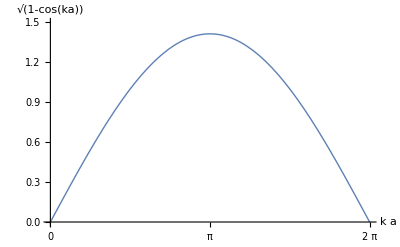

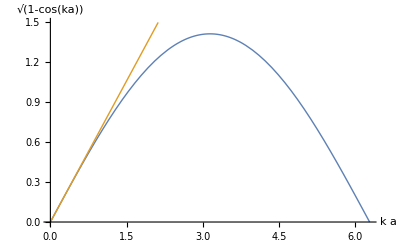

```mathematica
ClearAll[firstorder]
firstorder[y_] := (Series[Sqrt[1 - Cos[x]],{x,0,1}] // Normal) /. x -> y;
firstorder[y] // TraditionalForm
Plot[
Sqrt[1 - Cos[x]], {x, 0, 2 Pi}, Ticks->{{0,Pi,2Pi}, Automatic},
PlotStyle->Thick,
PlotRange->{Automatic, {0,1.5}},
AxesLabel -> {"k a" // fs, Sqrt[1 - Cos[ka]] //fs}
]
lecture21Fig2 = Plot[{
Sqrt[1 - Cos[x]],
firstorder[x]
} // Evaluate, {x, 0, 2 Pi}, 
PlotStyle->Thick,
PlotRange->{Automatic, {0,1.5}},
AxesLabel -> {"k a" // fs, Sqrt[1 - Cos[ka]] //fs}
]
```

```mathematica
peeters`exportForLatex["lecture21Fig2",lecture21Fig2]
```

{lecture21Fig2.eps,lecture21Fig2pn.png}